9-x^2

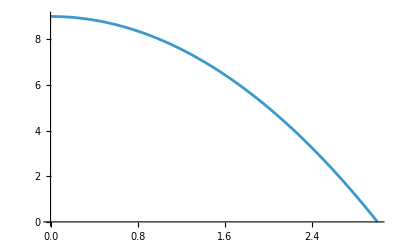

```mathematica
g=9-x^2
Plot[9 - x^2, {x, 0, 3}]
```

```mathematica
a=0;
b=3;
A=Integrate[g,{x,a,b}]
```

18

```mathematica
k=1/A
f=k*g
Integrate[f,{x,a,b}]
```

1/18

1/18 (9-x^2)

1

```mathematica
a=0;
b=1;
Integrate[f,{x,a,b}]
```

13/27

```mathematica
a=0;
b=2;
Integrate[f,{x,a,b}]
```

23/27

```mathematica
a=1;
b=2;
Integrate[f,{x,a,b}]
```

10/27

```mathematica
a=0;
b=x;
Integrate[f,{x,a,b}]
```

x/2-x^3/54

```mathematica
a=0;
b=3;
EV=Integrate[x*f,{x,a,b}]//N
Var=Integrate[(x-EV)^2*f,{x,a,b}]//N
Stdev=Sqrt[Var]//N
```

1.125

0.534375

0.73101

```mathematica
a=0
b=1
f=c(x^2+x)
Integrate[f,{x,a,b}]
Solve[Integrate[f,{x,a,b}]==1]
```

0

1

c (x+x^2)

(5 c)/6

{{c→6/5}}

1

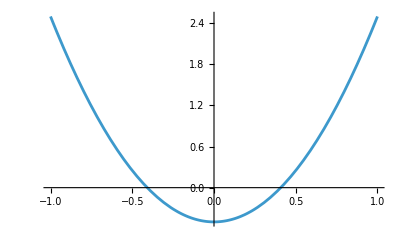

```mathematica
a=-1;
b=1;
f=3x^2-1/2;
Integrate[f,{x,a,b}]
Plot[f,{x,a,b}]
```

```mathematica
a=-1;
b=1;
f=-3x^2/32+3/8;
Integrate[f,{x,a,b}]
```

11/16